```mathematica
Clear["`*"]
k=20;
```

## Hide this

```mathematica
alpha=3.0/8.0;
a1=25.0/16.0;
a2=1.0/5.0;
a3=-1.0/80.0;
gamma01=3.210113927329531;
gamma10=2.21110473043239;
gamma12=42.08319933908019;
gamma21=1.557633196122124;
gamma23=6.482610425055064;
gamma32=-1.329341564172446;
gamma34=-2.465569273620743;
gamma43=-1.213703810247279;
gamma45=1.660769542489766;
gamma54=-0.1776191023391513;
gamma56=0.2232924886469337;
a00=-3.051444846761362;
a01=2.345334805372179;
a02=-0.8696582180114061;
a03=3.641381848342838;
a04=-3.399810121117448;
a05=1.792414554502852;
a06=-0.5246438812007604;
a07=0.0664258588731064;
a10=-4.873954900119216;
a12=-53.18177248515291;
a13=93.4348874201782;
a14=-52.74983250718357;
a15=22.56437298084277;
a16=-5.886555463761137;
a17=0.692854955195867;
a20=-0.2604486511132088;
a21=-1.943640425204907;
a23=-3.84806892990241;
a24=8.245332418591937;
a25=-2.779674691274779;
a26=0.6603673342280958;
a27=-0.0738670553247296;
a30=-0.05878600824425402;
a31=0.7074851396321982;
a32=-0.2983532234844736;
a34=1.491392318405186;
a35=-2.222455418896595;
a36=0.4240020577097782;
a37=-0.0432848651218399;
a40=0.05619441751764617;
a41=-0.4761142198435586;
a42=1.967293657743868;
a43=-2.297921866880887;
a45=-0.7202751534930111;
a46=1.865337479238859;
a47=-0.447823643536206;
a48=0.0533093292532889;
a50=-0.005353093751500729;
a51=0.04953262252336028;
a52=-0.2157074945553577;
a53=0.6319138819385537;
a54=-1.144234713147819;
a56=0.6783115550998231;
a57=0.005414306071706973;
a58=0.0001229358212328832;
```

```mathematica
(*Create and display a tridiagonal matrix with 3 boundary rows*)
triRowsLHS[i_,j_,D_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=6;
(*If[(i==1&&j==1)||(i==k&&j==k),gamma00,
If[(i==1&&j==2)||(i==k&&j==k-1),gamma01,*)
(*If[(i-1==j)&&(i<=numBoundaryRows||k-i>=numBoundaryRows),gamma[i-1,j-1]]*)
If[(i-1==j)&&(i<=numBoundaryRows),ToExpression["gamma"<>ToString[i-1]<>ToString[j-1]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["gamma"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(i<=numBoundaryRows),ToExpression["gamma"<>ToString[i-1]<>ToString[j-1]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["gamma"<>ToString[k-i]<>ToString[k-j]],

If[i-1==j, alpha,
If[i==j, 1,
If[i+1==j, alpha,
0]]]]]]]]
BoundTriMatrixLHS[D_,k_]:=Array[triRowsLHS[#1,#2,D,k]&,{k,k}]

LHS[k_]=BoundTriMatrixLHS[d,k];
LHS[k]//MatrixForm
```

(1 | gamma01 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
gamma10 | 1 | gamma12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | gamma21 | 1 | gamma23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | gamma32 | 1 | gamma34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | gamma43 | 1 | gamma45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | gamma54 | 1 | gamma56 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | alpha | 1 | alpha | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | alpha | 1 | alpha | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | alpha | 1 | alpha | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | alpha | 1 | alpha | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | alpha | 1 | alpha | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | alpha | 1 | alpha | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | alpha | 1 | alpha | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | alpha | 1 | alpha | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | gamma56 | 1 | gamma54 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | gamma45 | 1 | gamma43 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | gamma34 | 1 | gamma32 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | gamma23 | 1 | gamma21 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | gamma12 | 1 | gamma10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | gamma01 | 1)

```mathematica
(*Create and display a tridiagonal matrix with 3 boundary rows*)
triRowsRHS[i_,j_,D_,k_]:=Module[{numBoundaryRows},
If[i==1&&j==1,a00,
If[i==1&&j==2,a01,
If[i==1&&j==3,a02,
If[i==1&&j==4,a03,
If[i==1&&j==5,a04,
If[i==1&&j==6,a05,
If[i==1&&j==7,a06,
If[i==1&&j==8,a07,

If[i==2&&j==1,a10,
If[i==2&&j==3,a12,
If[i==2&&j==4,a13,
If[i==2&&j==5,a14,
If[i==2&&j==6,a15,
If[i==2&&j==7,a16,
If[i==2&&j==8,a17,

If[i==3&&j==1,a20,
If[i==3&&j==2,a21,
If[i==3&&j==4,a23,
If[i==3&&j==5,a24,
If[i==3&&j==6,a25,
If[i==3&&j==7,a26,
If[i==3&&j==8,a27,

If[i==4&&j==1,a30,
If[i==4&&j==2,a31,
If[i==4&&j==3,a32,
If[i==4&&j==5,a34,
If[i==4&&j==6,a35,
If[i==4&&j==7,a36,
If[i==4&&j==8,a37,

If[i==5&&j==1,a40,
If[i==5&&j==2,a41,
If[i==5&&j==3,a42,
If[i==5&&j==4,a43,
If[i==5&&j==6,a45,
If[i==5&&j==7,a46,
If[i==5&&j==8,a47,
If[i==5&&j==9,a48,

If[i==6&&j==1,a50,
If[i==6&&j==2,a51,
If[i==6&&j==3,a52,
If[i==6&&j==4,a53,
If[i==6&&j==5,a54,
If[i==6&&j==7,a56,
If[i==6&&j==8,a57,
If[i==6&&j==9,a58,



If[i==k&&j==k,-a00,
If[i==k&&j==k-1,-a01,
If[i==k&&j==k-2,-a02,
If[i==k&&j==k-3,-a03,
If[i==k&&j==k-4,-a04,
If[i==k&&j==k-5,-a05,
If[i==k&&j==k-6,-a06,
If[i==k&&j==k-7,-a07,

If[i==k-1&&j==k,-a10,
If[i==k-1&&j==k-2,-a12,
If[i==k-1&&j==k-3,-a13,
If[i==k-1&&j==k-4,-a14,
If[i==k-1&&j==k-5,-a15,
If[i==k-1&&j==k-6,-a16,
If[i==k-1&&j==k-7,-a17,

If[i==k-2&&j==k,-a20,
If[i==k-2&&j==k-1,-a21,
If[i==k-2&&j==k-3,-a23,
If[i==k-2&&j==k-4,-a24,
If[i==k-2&&j==k-5,-a25,
If[i==k-2&&j==k-6,-a26,
If[i==k-2&&j==k-7,-a27,

If[i==k-3&&j==k,-a30,
If[i==k-3&&j==k-1,-a31,
If[i==k-3&&j==k-2,-a32,
If[i==k-3&&j==k-4,-a34,
If[i==k-3&&j==k-5,-a35,
If[i==k-3&&j==k-6,-a36,
If[i==k-3&&j==k-7,-a37,

If[i==k-4&&j==k,-a40,
If[i==k-4&&j==k-1,-a41,
If[i==k-4&&j==k-2,-a42,
If[i==k-4&&j==k-3,-a43,
If[i==k-4&&j==k-5,-a45,
If[i==k-4&&j==k-6,-a46,
If[i==k-4&&j==k-7,-a47,
If[i==k-4&&j==k-8,-a48,

If[i==k-5&&j==k,-a50,
If[i==k-5&&j==k-1,-a51,
If[i==k-5&&j==k-2,-a52,
If[i==k-5&&j==k-3,-a53,
If[i==k-5&&j==k-4,-a54,
If[i==k-5&&j==k-6,-a56,
If[i==k-5&&j==k-7,-a57,
If[i==k-5&&j==k-8,-a58,



If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
BoundTriMatrixRHS[D_,k_]:=Array[triRowsRHS[#1,#2,D,k]&,{k,k}]

RHS[k_]=BoundTriMatrixRHS[d,k];
RHS[k]//MatrixForm
```

(a00 | a01 | a02 | a03 | a04 | a05 | a06 | a07 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a10 | 0 | a12 | a13 | a14 | a15 | a16 | a17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a20 | a21 | 0 | a23 | a24 | a25 | a26 | a27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a30 | a31 | a32 | 0 | a34 | a35 | a36 | a37 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a40 | a41 | a42 | a43 | 0 | a45 | a46 | a47 | a48 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a50 | a51 | a52 | a53 | a54 | 0 | a56 | a57 | a58 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a58 | -a57 | -a56 | 0 | -a54 | -a53 | -a52 | -a51 | -a50
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a48 | -a47 | -a46 | -a45 | 0 | -a43 | -a42 | -a41 | -a40
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a37 | -a36 | -a35 | -a34 | 0 | -a32 | -a31 | -a30
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a27 | -a26 | -a25 | -a24 | -a23 | 0 | -a21 | -a20
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a17 | -a16 | -a15 | -a14 | -a13 | -a12 | 0 | -a10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -a07 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

## Run this

1/((3.99439×10^-6+1.67066×10^-7 λ)^2)2.18899×10^101 (2.28509×10^-79-1.72898×10^-78 λ-6.35816×10^-79 λ^2-9.68935×10^-80 λ^3-1.28299×10^-80 λ^4-4.97001×10^-82 λ^5+2.93437×10^-83 λ^6-1.72646×10^-83 λ^7-4.47187×10^-84 λ^8-3.88073×10^-85 λ^9-1.12319×10^-86 λ^10+3.99242×10^-88 λ^11+3.50063×10^-89 λ^12+5.84076×10^-91 λ^13+1.96197×10^-93 λ^14+1.88528×10^-93 λ^15+1.57066×10^-94 λ^16+5.81496×10^-96 λ^17+1.17677×10^-97 λ^18+1.22681×10^-99 λ^19+4.86846×10^-102 λ^20+2.7472×10^-105 λ^21-4.4073×10^-105 λ^22-3.01384×10^-106 λ^23-8.41903×10^-108 λ^24-1.22352×10^-109 λ^25-8.39675×10^-112 λ^26+1.07668×10^-114 λ^27+7.34919×10^-116 λ^28+6.83704×10^-118 λ^29+3.53553×10^-120 λ^30+1.07622×10^-122 λ^31-7.28971×10^-126 λ^32-3.34857×10^-127 λ^33-1.91175×10^-129 λ^34-5.28264×10^-132 λ^35-8.34643×10^-135 λ^36-8.17561×10^-138 λ^37-1.71488×10^-141 λ^38+6.4124×10^-144 λ^39+2.64724×10^-147 λ^40+2.31667×10^-151 λ^41+6.15686×10^-157 λ^42)

-Graphics-

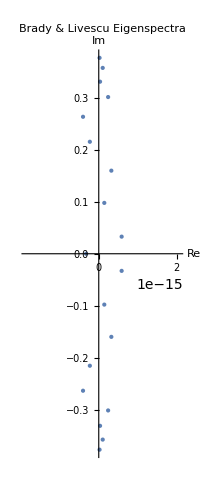

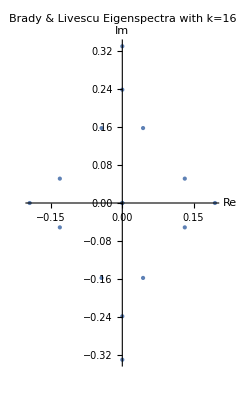

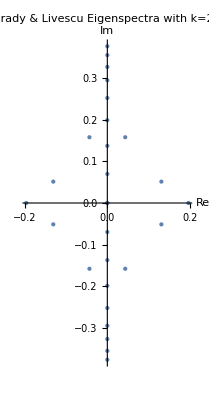

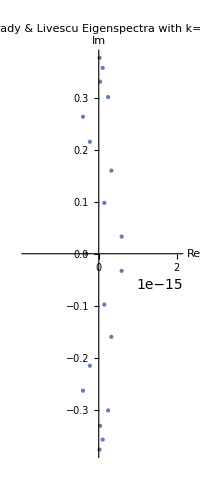

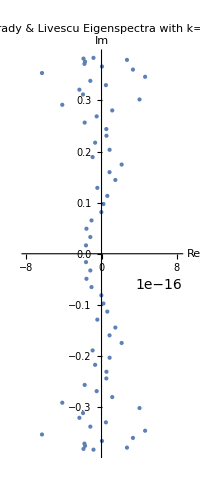

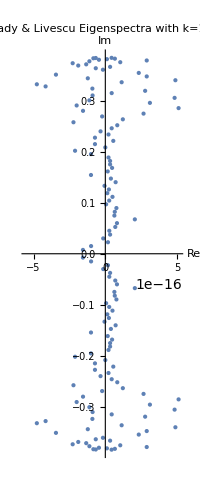

```mathematica
h=.1;
(*k=160;*)
size=29;

characteristicPolynomial[λ_]=Det[Inverse[LHS[size]]]*Det[RHS[size]-λ*h*LHS[size]]
Plot[characteristicPolynomial[λ],{λ,-20,20}]
eig[k_]:=Eigenvalues[Inverse[LHS[k]].RHS[k]]*h;
ComplexListPlot[eig[size],PlotLabel->"Brady & Livescu Eigenspectra",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[16],PlotLabel->"Brady & Livescu Eigenspectra with k=16",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[28],PlotLabel->"Brady & Livescu Eigenspectra with k=28",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[29],PlotLabel->"Brady & Livescu Eigenspectra with k=29",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[80],PlotLabel->"Brady & Livescu Eigenspectra with k=80",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
ComplexListPlot[eig[160],PlotLabel->"Brady & Livescu Eigenspectra with k=160",AxesLabel->{"Re","Im"},PlotStyle->{PointSize->Medium},AspectRatio->Full]
```